```mathematica
$Post = MatrixForm;
(*derive the projectile's position as a function of time*)
xhat = {1,0};
yhat = {0,1};
R2 = 120;
vInitial = {Vx,Vy} +  r0*omega*{-Sin[omega*t0-Pi/2],Cos[omega *t0 - Pi/2]};
p = vInitial * t + {0,-R};
startingValues = {Vx->1,Vy->1,r0->100,t0 -> 0,omega -> .01,R->105};
path[t_] = p /. startingValues
Thrower[t_] = R{-Sin[omega*t-Pi/2],Cos[omega *t - Pi/2]}/.startingValues
r = p.p
thetaR =  R* ArcTan[xhat.p,yhat.p]
```

Null

Null

Null

«4 more identical outputs»

(2. t
-105+1. t)

(105 Cos[0.01 t]
105 Sin[0.01 t])

t^2 (Vx+omega r0 Cos[omega t0])^2+(-R+t (Vy+omega r0 Sin[omega t0]))^2

```mathematica
Simplify[r]
```

t^2 (Vx+omega r0 Cos[omega t0])^2+(-R+t Vy+omega r0 t Sin[omega t0])^2

```mathematica
Simplify[thetaR]
```

R ArcTan[t (Vx+omega r0 Cos[omega t0]),-R+t Vy+omega r0 t Sin[omega t0]]

Null

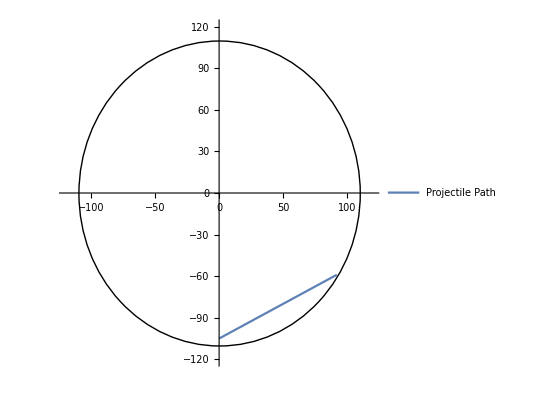

```mathematica
(*This is what our setup looks like. A ball is thrown at the bottom of the ship*)
parametric = ParametricPlot[{{1,0}.path[t],{0,1}.path[t]},{t,0,46},PlotRange->{{-R2,R2},{-R2,R2}},PlotLegends->{"Projectile Path"}];
Show[ parametric,Graphics[Circle[{0,0},110]],PlotRangeClipping->True]
```

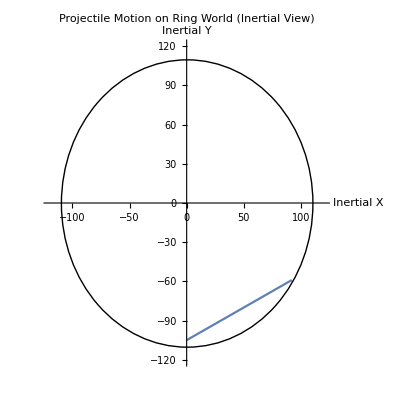

```mathematica
Show[%78,AxesLabel->{HoldForm[Inertial X],HoldForm[Inertial Y]},PlotLabel->HoldForm[Projectile Motion on Ring World (Inertial View)],LabelStyle->{GrayLevel[0]}]
```

√(4. t^2+(-105+1. t)^2)

ArcTan[105 Cos[0.01 t],105 Sin[0.01 t]]

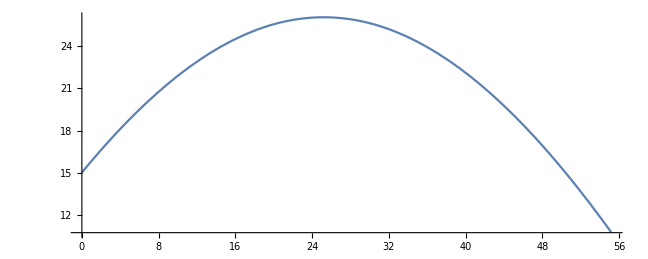

```mathematica
(*pvec is a vector that points to the ball from ship center*)
(*Thus distance from center is given by*)

(*Take the x and y component of projectile and plug it into tan(x,y) to get angle. Then add or subtract relative angle of the observer*)
(*in paper, refer the arctan xy mathematica function*)
(*call it \arctan(  ,  )*)
rMag[t_] = Sqrt[path[t].path[t]];
angleInRads[t_]= ArcTan[xhat.Thrower[t],yhat.Thrower[t]];
ParametricPlot[{R2 * angleInRads[t],R2 - rMag[t]},{t,0,46}]
```

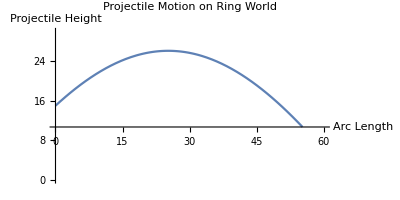

```mathematica
Show[%81,AxesLabel->{HoldForm[Arc Length],HoldForm[Projectile Height]},PlotLabel->HoldForm[Projectile Motion on Ring World],LabelStyle->{GrayLevel[0]},PlotRange->{{0,60},{0,30}}]
```

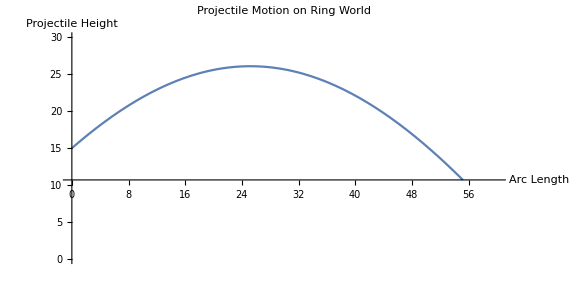

```mathematica
Show[%83,ImageSize->Large]
```

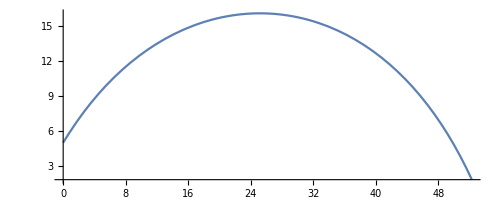

```mathematica
ParametricPlot[{110*((220. t Cos[0.01 Conjugate[t]]+110 (-110+1. t) Sin[0.01 Conjugate[t]])/(√(4. Abs[t]^2+Abs[-110+1. t]^2) √(12100 Abs[Cos[0.01 t]]^2+12100 Abs[Sin[0.01 t]]^2))),110 - rMag[t]},{t,0,45}]
```

```mathematica
Show[%285,ImageSize->Large]
```

Show::gtype: Out is not a type of graphics.

Show[%285,ImageSize→Large]